# Tools.wl Documentation

## Read Me!

Please extract this file and the Tools.ws file (Move it out of the zip folder)

For the package to work, please run the following command in a Mathematica notebook within the same directory (same folder):

```mathematica
If[!ValueQ[Tools`isLoaded],SetDirectory[NotebookDirectory[]]; <<Tools.wl;"Tools.ws loaded","Tools.ws already loaded"]
```

Tools.ws loaded

Once this is done in any Mathematica notebook, all commands should work in all notebooks until you quit Mathematica.  
This notebook is set up to automatically run the initialisation script on startup.

To makes sure that the package has loaded correctly, run a command like the one below:

```mathematica
?TurningPointForm
```

Also, if the software malfunctions, resulting in you losing a mark, I’m honestly really sorry, but I’m not a professional programmer, I’m not even that good at it, I’m just doing this for fun in my free time, so use this at your own risk.

### Note if editing/contributing

This notebook is set so that it will not prompt you to save automatically to save me pain. (Though i will probably live to regret doing this).
If you wish to revert this, press control+shit+o and navigate to Notebook Options > File Options:
-Graphics-

Change the top drop down to Selected Notebook:
-Graphics-

Then tick the box next to ClosingSaveDialog:
-Graphics-

## Commands

### NormalLine

Finds the normal to a line at a certain point

```mathematica
NormalLine[(x+2)^2-2,x,-1]
```

1/2 (-3-x)

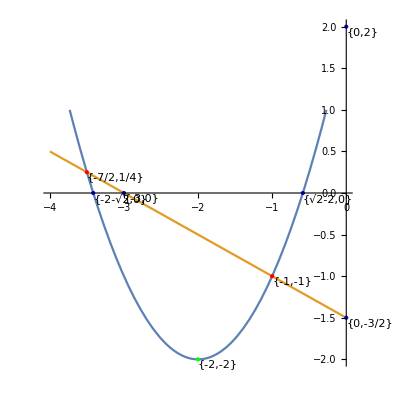

```mathematica
DetailedPlot[{(x+2)^2-2,1/2 (-3-x)},{x,-4,0},AspectRatio->Full,PlotRange-> {1,-3}]
```

### TangentLine

Finds the tangent to a curve at a certain point

```mathematica
TangentLine[expression, variable, point]
```

```mathematica
TangentLine[x^2-3x+2,x,4]
```

-14+5 x

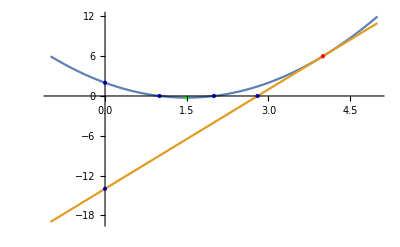

```mathematica
DetailedPlot[{x^2-3x+2,-14+5 x},{x,-1,5},Labels -> ""]
```

### Sine Rule

For side length b, and angles A and B, finds side length a.

```mathematica
SinRule[A °,{b, B °}] == a
```

```mathematica
SinRule[30°,{10,70°}]//N
```

5.32089

Remember to add ° symbol

You can also find angle A, for side lengths a,b and angle B

```mathematica
SinRuleAngle[a, {b, B °}]/°
```

```mathematica
SinRuleAngle[10,{13,60°}]/°//N
```

41.7724

Remember to divide by degrees. This is to allow for both degrees and radians to be used without two functions

### Cosine Rule

For angle A, and sides b,c, finds side a

```mathematica
CosRule[b, c, A °]
```

```mathematica
CosRule[10,20, 30°]//N
```

12.3931

For sides a,b, and c, find angle A

```mathematica
CosRuleAngle[a,b,c ]/°
```

```mathematica
CosRuleAngle[5,6,7]/Degree//N
```

44.4153

Remember to divide by degrees, this is to allow for both degrees and radians to be used in the same function.

### FindVariation

Gives you the variation for a given set of data. Note: you need generally need at least 3 data points

```mathematica
FindVariation[{{1,5},{8,2.5},{64,1.25}},x]
```

5/x^(1/3)

Optional argument for the tolerances of rationalizing, to turn rationalizing off, put 0 there instead.

```mathematica
FindVariation[{{1,5},{8,2.5},{64,1.25}},x,0]
```

5./x^0.333333

You can also do joint variation. (Make sure you put data, and variables in the same order)
I.e FindVariation[{x1,y1,result1},...},{x,y}]

```mathematica
FindVariation[{{2,10,15/2},{3,4,4/3},{5,50,6}},{x,z}]
```

(3 z)/x^2

An example of what happens when you mess with tolerances:

```mathematica
FindVariation[{{2,10,15/2},{3,4,4/3},{5,50,6}},{x,z},1]
```

(2 z)/x

### DetailedPlot

Works the same as Plot, but adds intercepts, intersections, and stationary points.

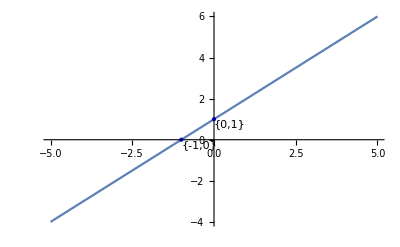

```mathematica
DetailedPlot[x+1,{x,-5,5}]
```

Types of points are colour coded:
Intersections: Red
Stationary Points: Green
Axes Intercepts: Blue

In the case where 1 point may be 2 types, priority is Stationary Points > Intersections > Axes Intercepts

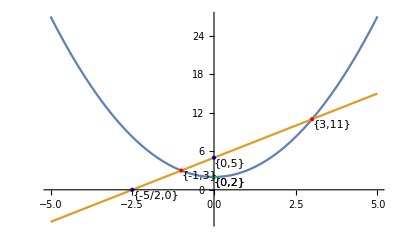

```mathematica
DetailedPlot[{x^2+2,2x+5},{x,-5,5}]
```

If you you wish to see labels in decimal form, use DecimalPlaces → True, or DecimalPlaces → n, for n number of decimal places

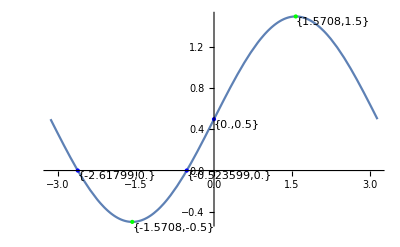

```mathematica
DetailedPlot[Sin[x]+1/2,{x,-π,π},DecimalPlaces -> True]
```

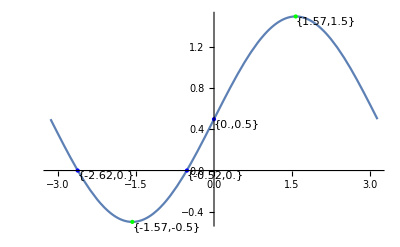

```mathematica
DetailedPlot[Sin[x]+1/2,{x,-π,π},DecimalPlaces -> 2]
```

As you can see, it can get a little cluttered:

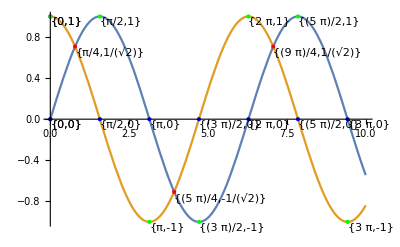

```mathematica
DetailedPlot[{Sin[x],Cos[x]},{x,0,10}]
```

If labels are appearing off the graph, you can double click the graph, and drag them back on.

If it gets too cluttered, you can filter which types of labels are shown with the Labels argument:

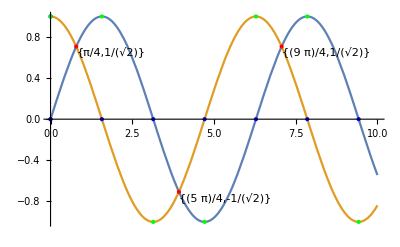

```mathematica
DetailedPlot[{Sin[x],Cos[x]},{x,0,10},Labels-> "Intersections"]
```

Valid arguments are “Intercepts”, “Intersections”, or “Stationary” (For stationary points)

If you wish to show 2 types of labels, simply use a list.

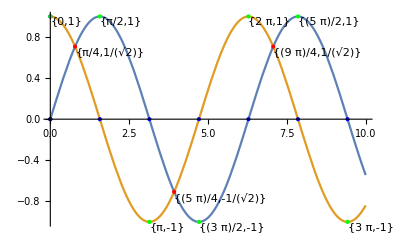

```mathematica
DetailedPlot[{Sin[x],Cos[x]},{x,0,10},Labels-> {"Intersections","Stationary"}]
```

You can also change the offset of the labels, with the argument LabelOffset → {x,y}
(It might not move the direction you expect. Play around with it a bit first.)

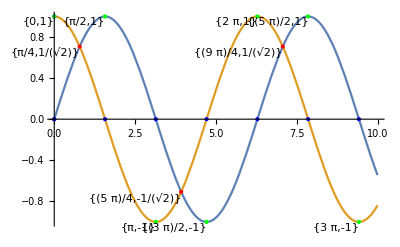

```mathematica
DetailedPlot[{Sin[x],Cos[x]},{x,0,10},Labels-> {"Intersections","Stationary"},LabelOffset -> {1,1}]
```

### TurningPointForm

Converts a quadratic into turning point form.

```mathematica
TurningPointForm[x,x^2+16x+9]
```

-55+(8+x)^2

Don’t put something that isn’t a quadratic, it will make me very sad :(

```mathematica
TurningPointForm[x,2]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

### RestrictedFunction

Creates a function with a restricted domain/condition.

```mathematica
RestrictedFunction[var,expresion,condition]
```

```mathematica
RestrictedFunction[x,x+1,x>1]
```

Function[x,ConditionalExpression[1+x, x>1]]

```mathematica
f:=RestrictedFunction[x,x+1,x>1]
```

```mathematica
f[t]
```

ConditionalExpression[1+t, t>1]

```mathematica
f[0]
```

Undefined

For the purposes of an inverse function:

```mathematica
h1 := RestrictedFunction[x,(x-2)^2+2,x≥2]
```

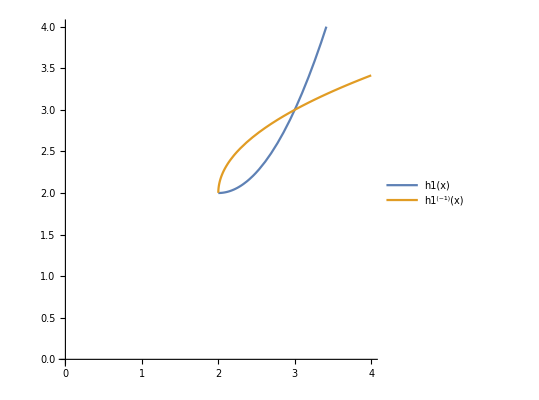

```mathematica
Plot[{h1[x],InverseFunction[h1][x]},{x,0,4},AspectRatio->Automatic,PlotLegends->"Expressions",PlotRange->{0,4},AxesOrigin->{0,0}]
```

```mathematica
h2:=RestrictedFunction[x,(x-2)^2+2,x<=2]
```

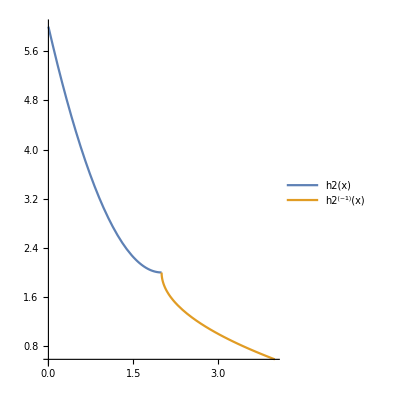

```mathematica
Plot[{h2[x],InverseFunction[h2][x]},{x,0,4},AspectRatio->Full,PlotLegends->"Expressions"]
```

### SolveTriangle

This will solve for missing side lengths and angles of a triangles. At least 3 values and 1 side length is necessary to solve.
(Function is set to use degrees by default)

```mathematica
SolveTriangle[{a,b,c},{A,B,CC}]
```

a,b and c are side lengths.
A,B, and CC are angles.

(CC is used because C is a built in variable)

```mathematica
(*Sine Rule Question*)
SolveTriangle[{12,b,c},{A,59,73}]//N
```

{{A→48.,b→13.8412,c→15.442}}

```mathematica
(*Cosine Rule Question*)
SolveTriangle[{a,16,30},{60,B,CC}]//N
```

{{a→26.,B→32.2042,CC→87.7958}}

You can also use radians with the settings Degrees → False

```mathematica
SolveTriangle[{a,16,30},{Pi /3,B,CC},Degrees -> False]//N
```

{{a→26.,B→0.56207,CC→1.53233}}

The setting Area → True will output the area of the triangle.(You will still need placeholder symbols in place of unknown sides/angles)

```mathematica
SolveTriangle[{2,3,4},{a,b,c},Area->True]//N
```

{2.90474}

### FTest

This will check whether a function satisfies a list of conditions.

```mathematica
FTest[exp,conditions,variableName,functionName]
```

```mathematica
FTest[x+1,{h[2]==3,h[3]<2},x,h]
```

h[2]==3 is True
h[3]<2 is False

```mathematica
FTest[1/(x-1),{h[x]h[-x]==-h[x^2],h[x] + h[-x]==2h[x^2],h[x]^2==h[x^2]},x,h]
```

h[-x] h[x]==-h[x^2] is True
h[-x]+h[x]==2 h[x^2] is True
h[x]^2==h[x^2] is False

You also add assumptions for the test

```mathematica
FTest[Log[x],{h[a]+ h[b] ==h[a *b]},x,h,Assumptions->{a >0,b>0}]
```

h[a]+h[b]==h[a b] is True

From this point onwards, I have gotten lazy with documenting, so good luck :/

### RFTest

Like FTest, but instead checks whether different functions satisfy a condition.

```mathematica
RFTest[{12x,12x^2},g[a]==g[-a],x,g]
```

12 x DOES NOT satisfy condition
12 x^2 DOES satisfy condition

### Surdify

Replaces fractional powers with the surd equivalent. Note that some constants will still have a fractional power if they result in  real number.
Also note that you cannot put surdify directly into a plot command. You must copy paste its output, or use // Evaluate

```mathematica
g[x_]:=3(x-2)^3+2
```

```mathematica
InverseFunction[g][x]//Surdify
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

2+(-2+x)^(1/3)/3^(1/3)

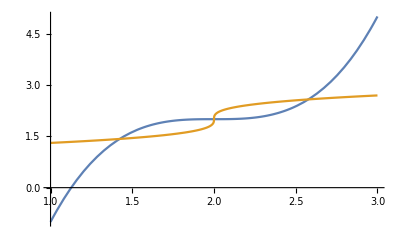

```mathematica
Plot[{g[x],InverseFunction[g][x]//Surdify//Evaluate},{x,1,3}]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

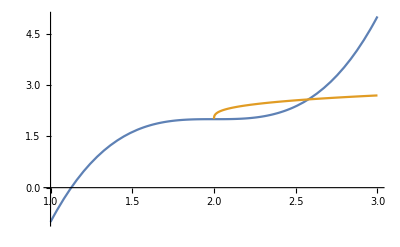

```mathematica
Plot[{g[x],InverseFunction[g][x]},{x,1,3}]
```

### AreaApproximation

```mathematica
AreaApproximation[exp,{var,start,end},step]
```

```mathematica
AreaApproximation[x^2 ,{x,1,4},1]
```

30

```mathematica
AreaApproximation[x^2,{x,0,3}]
```

14

```mathematica
Integrate[x^2,{x,0,4}]//N
```

21.3333